## Утилиты

### Работа с файловой системой

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Alex\Documents\Visual Studio Projects\BMSTU\Diploma\Boltzmann_1D_Solver\Boltzmann_1D_Solver

### Получение данных

#### Получение макропараметров

```mathematica
ReadLastBgk1Results[testDirName_String]:=Module[{path,t,n,u1,T,q1,x},
path="output\\bgk1d\\"<>testDirName;
t=Last@First@Import[path<>"\\t_levels.txt","Table"];
x=Last@Import[Evaluate@path<>"\\x_1_levels.txt","Table"];
n=Last@Import[Evaluate@path<>"\\n.txt","Table"];
u1=Last@Import[Evaluate@path<>"\\u_1.txt","Table"];
T=Last@Import[Evaluate@path<>"\\T.txt","Table"];
q1=Last@Import[Evaluate@path<>"\\q_1.txt","Table"];
Evaluate@<|
"t"->t,
"x"->x,
"n"->n,
"u_1"->u1,
"T"->T,
"q_1"->q1
|>
]
```

```mathematica
ReadFirstBgk1Results[testDirName_String]:=Module[{path,t,n,u1,T,q1,x},
path="output\\bgk1d\\"<>testDirName;
t=First@First@Import[path<>"\\t_levels.txt","Table"];
x=First@Import[Evaluate@path<>"\\x_1_levels.txt","Table"];
n=First@Import[Evaluate@path<>"\\n.txt","Table"];
u1=First@Import[Evaluate@path<>"\\u_1.txt","Table"];
T=First@Import[Evaluate@path<>"\\T.txt","Table"];
q1=First@Import[Evaluate@path<>"\\q_1.txt","Table"];
Evaluate@<|
"t"->t,
"x"->x,
"n"->n,
"u_1"->u1,
"T"->T,
"q_1"->q1
|>
]
```

```mathematica
ReadLastBgk1Results["testSmall"][["x"]]
```

{-0.833333,-0.833333,-0.5,-0.166667,0.166667,0.5,0.833333}

```mathematica
ReadAllBgk1Results[testDirName_String]:=Module[{path,ts,ns,u1s,Ts,q1s,xs},
path="output\\bgk1d\\"<>testDirName;
ts=First@Import[path<>"\\t_levels.txt","Table"];
xs=Import[Evaluate@path<>"\\x_1_levels.txt","Table"];
ns=Import[Evaluate@path<>"\\n.txt","Table"];
u1s=Import[Evaluate@path<>"\\u_1.txt","Table"];
Ts=Import[Evaluate@path<>"\\T.txt","Table"];
q1s=Import[Evaluate@path<>"\\q_1.txt","Table"];
Table[Module[{t,n,u1,T,q1,x},
t=ts[[i]];
x=xs[[i]];
n=ns[[i]];
u1=u1s[[i]];
T=Ts[[i]];
q1=q1s[[i]];
Evaluate@<|
"t"->t,
"x"->x,
"n"->n,
"u_1"->u1,
"T"->T,
"q_1"->q1
|>
],{i,Length@ts}]
]
```

#### Получение функций распределений

```mathematica
ReadLastBgk1Distributions[testDirName_String]:=Module[{path,t,h,g,x,xi},
path="output\\bgk1d\\"<>testDirName;
t=Last@First@Import[path<>"\\t_levels.txt","Table"];
x=Last@Import[Evaluate@path<>"\\x_1_levels.txt","Table"];
xi=Last@Import[Evaluate@path<>"\\xi_1_levels.txt","Table"];
h=Last@SequenceSplit[Import[Evaluate@path<>"\\h.txt","Table"],{{}}];
g=Last@SequenceSplit[Import[Evaluate@path<>"\\g.txt","Table"],{{}}];
Evaluate@<|
"t"->t,
"x"->x,
"xi"->xi,
"h"->h,
"g"->g
|>
]
```

```mathematica
ReadLastBgk1Distributions["testCrash"]
```

<|t→t$66514,x→x$66514,xi→xi$66514,h→h$66514,g→g$66514|>

```mathematica
First@SequenceSplit[{{a,f},{a,d},{},{a},{},{}},{{}}]
```

{{a,f},{a,d}}

```mathematica
ReadAllBgk1Distributions[testDirName_String]:=Module[{path,ts,hs,gs,xs,xis},
path="output\\bgk1d\\"<>testDirName;
ts=First@Import[path<>"\\t_levels.txt","Table"];
xs=Import[Evaluate@path<>"\\x_1_levels.txt","Table"];
xis=Import[Evaluate@path<>"\\xi_1_levels.txt","Table"];
hs=SequenceSplit[Import[Evaluate@path<>"\\h.txt","Table"],{{}}];
gs=SequenceSplit[Import[Evaluate@path<>"\\g.txt","Table"],{{}}];

Table[Module[{t,h,g,x,xi},
t=ts[[i]];
x=xs[[i]];
xi=xis[[i]];
h=hs[[i]];
g=gs[[i]];
Evaluate@<|
"t"->t,
"x"->x,
"xi"->xi,
"h"->h,
"g"->g
|>
],{i,Length@ts}]
]
```

## Построение графиков

### 1D

```mathematica
Macroparameters1dPlot[params_Association]:=Module[{Nx},
Nx=Length@params[["x"]];
Grid[{
{
ListPlot[Table[{params[["x"]][[i]],params[["n"]][[i]]},{i,Nx}],AxesLabel->{"x","n"},PlotRange->Full],
ListPlot[Table[{params[["x"]][[i]],params[["u_1"]][[i]]},{i,Nx}],AxesLabel->{"x","u_1"},PlotRange->Full]
},
{
ListPlot[Table[{params[["x"]][[i]],params[["T"]][[i]]},{i,Nx}],AxesLabel->{"x","T"},PlotRange->Full],
ListPlot[Table[{params[["x"]][[i]],params[["q_1"]][[i]]},{i,Nx}],AxesLabel->{"x","q_1"},PlotRange->Full]
}
}]
]
```

```mathematica
Macroparameter1dPlot[params_Association,paramName_String]:=Module[{Nx},
Nx=Length@params[["x"]];
ListPlot[Table[{params[["x"]][[i]],params[[paramName]][[i]]},{i,Nx}],AxesLabel->{"x",paramName},PlotRange->Full]
]
```

```mathematica
Distribution1dPrint[params_Association]:=Module[{Nx,Nxi},
Nx=Length@params[["x"]];
Nxi=Length@params[["xi"]];
Grid[{
{
ListPointPlot3D[Table[{params[["x"]][[i]],params[["xi"]][[j]],params[["h"]][[i,j]]},{i,Nx},{j,Nxi}],AxesLabel->{"x","xi","h"}],
Manipulate[Grid[Transpose@{{
params[["x"]][[i]],
ListPlot[Table[{params[["xi"]][[j]],params[["h"]][[i,j]]},{j,Length@params[["xi"]]}],AxesLabel->{"xi","h"},PlotRange->Full]
}}],{i,1,Length@params[["x"]],1}],
Manipulate[Grid[Transpose@{{
params[["xi"]][[j]],
ListPlot[Table[{params[["x"]][[i]],params[["h"]][[i,j]]},{i,Length@params[["x"]]}],AxesLabel->{"x","h"},PlotRange->Full]
}}],{j,1,Length@params[["xi"]],1}]
}
,
{
ListPointPlot3D[Table[{params[["x"]][[i]],params[["xi"]][[j]],params[["g"]][[i,j]]},{i,Nx},{j,Nxi}],AxesLabel->{"x","xi","g"}],
Manipulate[Grid[Transpose@{{
params[["x"]][[i]],
ListPlot[Table[{params[["xi"]][[j]],params[["g"]][[i,j]]},{j,Length@params[["xi"]]}],AxesLabel->{"xi","g"},PlotRange->Full]
}}],{i,1,Length@params[["x"]],1}],
Manipulate[Grid[Transpose@{{
params[["xi"]][[j]],
ListPlot[Table[{params[["x"]][[i]],params[["g"]][[i,j]]},{i,Length@params[["x"]]}],AxesLabel->{"x","g"},PlotRange->Full]
}}],{j,1,Length@params[["xi"]],1}]
}
}]
]
```

## БГК 1

### Распад разрыва для плотности

#### Последний временной слой

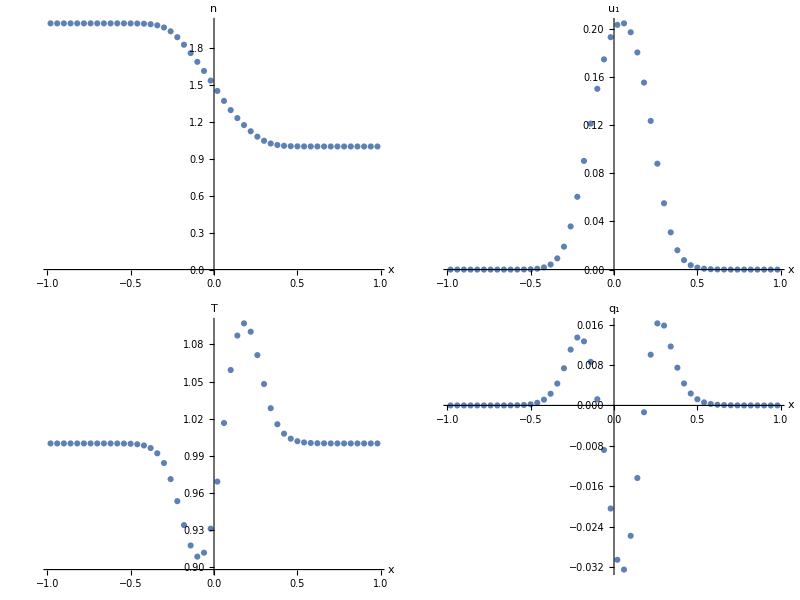

-Graphics3D- |  | 
-Graphics3D- |  |

Part::partd: Part specification x$204027⟦37⟧ is longer than depth of object.

Part::partd: Part specification xi$204027⟦23⟧ is longer than depth of object.

Part::partd: Part specification x$204027⟦24⟧ is longer than depth of object.

Part::partd: Part specification xi$204027⟦1⟧ is longer than depth of object.

Part::partd: Part specification x$204027⟦37⟧ is longer than depth of object.

Part::partd: Part specification xi$204027⟦1⟧ is longer than depth of object.

Part::partd: Part specification x$204027⟦37⟧ is longer than depth of object.

Part::partd: Part specification xi$204027⟦23⟧ is longer than depth of object.

Part::partd: Part specification x$204027⟦24⟧ is longer than depth of object.

Part::partd: Part specification xi$204027⟦1⟧ is longer than depth of object.

Part::partd: Part specification x$204027⟦37⟧ is longer than depth of object.

```mathematica
Module[{params},
params=ReadLastBgk1Results["testDensity"];
Macroparameters1dPlot[params]
]
Module[{params},
params=ReadLastBgk1Distributions["testDensity"];
Distribution1dPrint[params]
]
```

#### Временной промежуток перед концом

```mathematica
DynamicModule[{params},
params=ReadAllBgk1Results["testDensityMultiple"];
Export["testDensityMultiple.mp4",Table[Macroparameters1dPlot[params[[i]]],{i,1,40,1}]];

Manipulate[Macroparameters1dPlot[params[[i]]],{i,1,Length@params,1}]
]
(*
DynamicModule[{params},
params=ReadAllBgk1Distributions["testDensityMultiple"];
Manipulate[Distribution1dPrint[params[[i]]],{i,1,Length@params,1}]
]*)
```

### Распад разрыва для плотности при свободно молекулярном течении

#### Последний временной слой

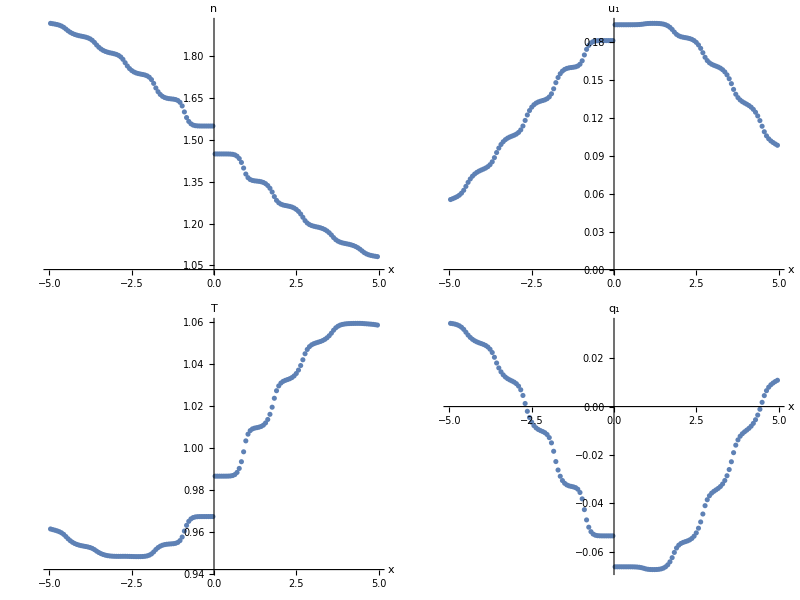

-Graphics3D- |  | 
-Graphics3D- |  |

```mathematica
Module[{params},
params=ReadLastBgk1Results["testFreeMoleculeDensity"];
Macroparameters1dPlot[params]
]
Module[{params},
params=ReadLastBgk1Distributions["testFreeMoleculeDensity"];
Distribution1dPrint[params]
]
```

#### Макропараметры на всем временном промежутке

```mathematica
DynamicModule[{params},
params=ReadAllBgk1Results["testFreeMoleculeDensity"];
Export["testFreeMoleculeDensity.mp4",Table[Macroparameters1dPlot[params[[i]]],{i,1,Length@params,1}]];

Manipulate[Macroparameters1dPlot[params[[i]]],{i,1,Length@params,1}]
]
(*
DynamicModule[{params},
params=ReadAllBgk1Distributions["testDensityMultiple"];
Manipulate[Distribution1dPrint[params[[i]]],{i,1,Length@params,1}]
]*)
```

#### Макропараметры на всем временном промежутке в случае сдвига

```mathematica
DynamicModule[{params},
params=ReadAllBgk1Results["testFreeMoleculeDensityShifted"];
Export["testFreeMoleculeDensityShifted.mp4",Table[Macroparameters1dPlot[params[[i]]],{i,1,40,1}]];

Manipulate[Macroparameters1dPlot[params[[i]]],{i,1,Length@params,1}]
]
(*
DynamicModule[{params},
params=ReadAllBgk1Distributions["testDensityMultiple"];
Manipulate[Distribution1dPrint[params[[i]]],{i,1,Length@params,1}]
]*)
```

```mathematica
DynamicModule[{params},
params=ReadAllBgk1Results["testFreeMoleculeDensityShifted"];
Export["testFreeMoleculeDensityShiftedExpected.mp4",Table[Show[Macroparameter1dPlot[params[[i]],"n"],Plot[1+Erf[-(x-1)/(params[[i]][["t"]])],{x,-5,5}]],{i,2,Length@params-1,1}]];

Manipulate[Show[Macroparameter1dPlot[params[[i]],"n"],Plot[1+Erf[-x01/(params[[i]][["t"]])],{x,-5,5}]],{i,2,Length@params-1,1}]
]
```